```mathematica
notes={9,10,14,12,10,9,7,0,5,7,9,10,9,7};durées={t,t,t,t,t/2,t/2,t,t,t,t,t,t/2,t/2,4t};
```

```mathematica
timbre=Table[z,{i,14}]
```

{z,z,z,z,z,z,z,z,z,z,z,z,z,z}

```mathematica
melodie=Transpose[{notes-6,durées,timbre}]
```

{{3,t,z},{4,t,z},{8,t,z},{6,t,z},{4,t/2,z},{3,t/2,z},{1,t,z},{-6,t,z},{-1,t,z},{1,t,z},{3,t,z},{4,t/2,z},{3,t/2,z},{1,4 t,z}}

```mathematica
m=SoundNote@@@melodie/.{t->0.33,z->"Violin"}
```

{SoundNote[3,0.33,Violin],SoundNote[4,0.33,Violin],SoundNote[8,0.33,Violin],SoundNote[6,0.33,Violin],SoundNote[4,0.165,Violin],SoundNote[3,0.165,Violin],SoundNote[1,0.33,Violin],SoundNote[-6,0.33,Violin],SoundNote[-1,0.33,Violin],SoundNote[1,0.33,Violin],SoundNote[3,0.33,Violin],SoundNote[4,0.165,Violin],SoundNote[3,0.165,Violin],SoundNote[1,1.32,Violin]}

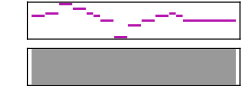

```mathematica
Sound[m]
```

```mathematica
EmitSound[Sound[m]]
```

```mathematica
Export["pastorale.WAV",EmitSound[Sound[m]]]
```

Export::nodta: Null contains no data that can be exported to the WAV format.

$Failed

```mathematica
Export["pastorale.WAV",Sound[m]]
```

First::normal: Nonatomic expression expected at position 1 in First[None].

$Failed

```mathematica
notes=   {4,  4,5,5,7, 7,    5,       4,    2,  None,5,  5,7,9,11,12,11,      9, 7,   None};
durées={4t,t,t,t,t,3t,t/2,t/2,3t, t,    4t,t,t,t,t,3t,t/2,t/2,3t, t};
```

```mathematica
melodie=Transpose[{notes,durées}]
```

{{7,4 t},{7,t},{8,t},{8,t},{10,t},{10,3 t},{8,t/2},{7,t/2},{5,3 t},{3+None,t},{8,4 t},{8,t},{10,t},{12,t},{14,t},{15,3 t},{14,t/2},{12,t/2},{10,3 t},{3+None,t}}

```mathematica
m=SoundNote@@@melodie/.{t->0.33}
```

{SoundNote[7,1.32],SoundNote[7,0.33],SoundNote[8,0.33],SoundNote[8,0.33],SoundNote[10,0.33],SoundNote[10,0.99],SoundNote[8,0.165],SoundNote[7,0.165],SoundNote[5,0.99],SoundNote[3+None,0.33],SoundNote[8,1.32],SoundNote[8,0.33],SoundNote[10,0.33],SoundNote[12,0.33],SoundNote[14,0.33],SoundNote[15,0.99],SoundNote[14,0.165],SoundNote[12,0.165],SoundNote[10,0.99],SoundNote[3+None,0.33]}

```mathematica
Sound[m]
```

Sound[{SoundNote[7,1.32],SoundNote[7,0.33],SoundNote[8,0.33],SoundNote[8,0.33],SoundNote[10,0.33],SoundNote[10,0.99],SoundNote[8,0.165],SoundNote[7,0.165],SoundNote[5,0.99],SoundNote[3+None,0.33],SoundNote[8,1.32],SoundNote[8,0.33],SoundNote[10,0.33],SoundNote[12,0.33],SoundNote[14,0.33],SoundNote[15,0.99],SoundNote[14,0.165],SoundNote[12,0.165],SoundNote[10,0.99],SoundNote[3+None,0.33]}]

```mathematica
notes=   {4,    4,       5,     5,       7,     7,         5,       4,    2,    5,  5,7,9,11,12,11,      9, 7};
durées={2t,t/2,t/2,t/2,t/2,3t/2,t/4,t/4,2t, 2t,t/2,t/2,t/2,t/2,3t/2,t/4,t/4,2t};
```

```mathematica
melodie=Transpose[{notes,durées}]
```

{{4,2 t},{4,t/2},{5,t/2},{5,t/2},{7,t/2},{7,(3 t)/2},{5,t/4},{4,t/4},{2,2 t},{5,2 t},{5,t/2},{7,t/2},{9,t/2},{11,t/2},{12,(3 t)/2},{11,t/4},{9,t/4},{7,2 t}}

```mathematica
m=SoundNote@@@melodie/.{t->0.66}
```

{SoundNote[4,1.32],SoundNote[4,0.33],SoundNote[5,0.33],SoundNote[5,0.33],SoundNote[7,0.33],SoundNote[7,0.99],SoundNote[5,0.165],SoundNote[4,0.165],SoundNote[2,1.32],SoundNote[5,1.32],SoundNote[5,0.33],SoundNote[7,0.33],SoundNote[9,0.33],SoundNote[11,0.33],SoundNote[12,0.99],SoundNote[11,0.165],SoundNote[9,0.165],SoundNote[7,1.32]}

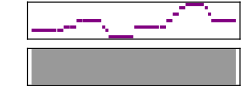

```mathematica
Sound[m]
```